```mathematica
param={m->1,k->0.1,g->9.8, xs0->-100,ys0->100,α->π-0.9,β->-1,u0->30,v0->34,xb0->0,yb0->0};
ux=u0 Cos[β];
uy=u0 Sin[β];
eqs1=m xs''[t]+k xs'[t];
eqs2=m ys''[t]+k ys'[t]+m g;
vx=v0 Cos[α];
vy=v0 Sin[α];
eqb1=m xb''[t]+k xb'[t];
eqb2=m yb''[t]+k yb'[t]+ m g;
```

```mathematica
sol1=NDSolve[{eqs1==0,eqs2==0,xs[0]==xs0,ys[0]==ys0,xs'[0]==ux,ys'[0]==uy}/.param,{xs[t],ys[t]},{t,0,10}];
sol2=NDSolve[{eqb1==0,eqb2==0,xb[0]==xb0,yb[0]==yb0,xb'[0]==vx,yb'[0]==vy}/.param,{xb[t],yb[t]},{t,0,10}];
```

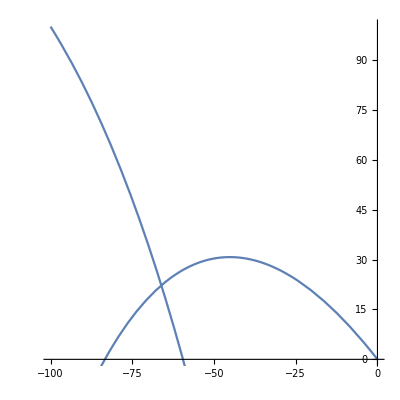

```mathematica
Show[ParametricPlot[Evaluate[{xs[t],ys[t]}/.sol1],{t,0,10},PlotRange->{{-100,0},{0,100}}],ParametricPlot[Evaluate[{xb[t],yb[t]}/.sol2],{t,0,10}]]
```

```mathematica
FindRoot[{xb[t]==xs[t]&& yb[t]==ys[t]}/.sol2/.sol1/.param,{t,0}]
```

FindRoot::nveq: The number of equations does not match the number of variables in FindRoot[{xb[«1»]==xs[«1»]&&yb[«1»]==ys[«1»]}/.sol2/.sol1/.param,{t,0}].

FindRoot[{xb[t]==xs[t]&&yb[t]==ys[t]}/.sol2/.sol1/.param,{t,0}]

```mathematica
FindRoot[{Exp[x-2]==y,y^2==x},{{x,1},{y,1}}]
```

{x→0.019026,y→0.137935}

```mathematica
For[i=xb0/.param,i>xs0/.param,i-=0.1,
FindRoot[{xs[t]==i}/.sol1,{t,0}]
]
```

```mathematica
sl1=DSolve[{eqs1==0,eqs2==0,xs[0]==xs0,ys[0]==ys0,xs'[0]==ux,ys'[0]==uy},{xs[t],ys[t]},t]
sl2=DSolve[{eqb1==0,eqb2==0,xb[0]==xb0,yb[0]==yb0,xb'[0]==vx,yb'[0]==vy},{xb[t],yb[t]},t]
```

{{xs[t]→(ⅇ^(-(k t)/m) (ⅇ^((k t)/m) k xs0-m u0 Cos[β]+ⅇ^((k t)/m) m u0 Cos[β]))/k,ys[t]→(ⅇ^(-(k t)/m) (-g m^2+ⅇ^((k t)/m) g m^2-ⅇ^((k t)/m) g k m t+ⅇ^((k t)/m) k^2 ys0-k m u0 Sin[β]+ⅇ^((k t)/m) k m u0 Sin[β]))/k^2}}

{{xb[t]→(ⅇ^(-(k t)/m) (ⅇ^((k t)/m) k xb0-m v0 Cos[α]+ⅇ^((k t)/m) m v0 Cos[α]))/k,yb[t]→(ⅇ^(-(k t)/m) (-g m^2+ⅇ^((k t)/m) g m^2-ⅇ^((k t)/m) g k m t+ⅇ^((k t)/m) k^2 yb0-k m v0 Sin[α]+ⅇ^((k t)/m) k m v0 Sin[α]))/k^2}}

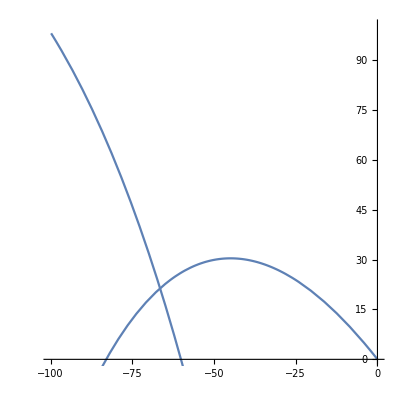

```mathematica
Show[ParametricPlot[{62.0 ⅇ^(-0.1 t) (-2.61+1. ⅇ^(0.1 t)),-98. ⅇ^(-0.1 t) (7.4-8.4 ⅇ^(0.1 t)+1. ⅇ^(0.1 t) t)},{t,0,10},PlotRange->{{-100,0},{0,100}}],ParametricPlot[{-211.3 ⅇ^(-0.1 t) (-1.+1. ⅇ^(0.1 t)),-98. ⅇ^(-0.1 t) (12.7-12.7 ⅇ^(0.1 t)+1. ⅇ^(0.1 t) t)},{t,0,10}]]
```

```mathematica
x=sl1[[1]][[1]]
```

xs[t]→62.0907 ⅇ^(-0.1 t) (-2.61055+1. ⅇ^(0.1 t))

```mathematica
Solve[62 ⅇ^(-0.1 t) (-2.6+1. ⅇ^(0.1 t))==n,t];
τ1=-10  Log[0.00624 (62- n)] ;
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-10 Log[0.00624 (62-n)]

```mathematica
ps=-98 ⅇ^(-0.1 t) (7.4-8.4 ⅇ^(0.1 t)+ ⅇ^(0.1 t) t)/.t->τ1;
```

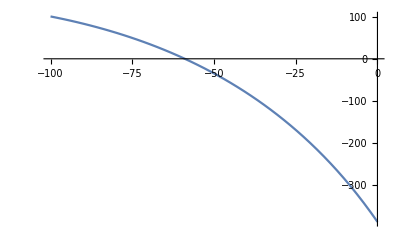

```mathematica
Plot[ps,{n,-100,0}]
```

```mathematica
Solve[-211.3 ⅇ^(-0.1 t) (-1.+1. ⅇ^(0.1 t))==n,t];
τ2=-10Log[-0.0047326076668(-211.3- n)];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
pb=-98. ⅇ^(-0.1 t) (12.7-12.7 ⅇ^(0.1 t)+1. ⅇ^(0.1 t) t)/.t->τ2;
```

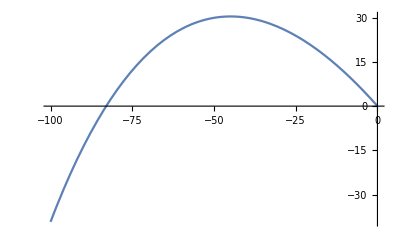

```mathematica
Plot[pb,{n,-100,0}]
```

```mathematica
FindRoot[pb==ps,{n,-80}]
```

{n→-65.5102}

```mathematica
FindRoot
```

```mathematica
Solve[(ⅇ^(-(k t)/m) (ⅇ^((k t)/m) k xs0-m u0 Cos[β]+ⅇ^((k t)/m) m u0 Cos[β]))/k==n,t]
```

{{t→ConditionalExpression[(m (2 ⅈ π C[1]+Log[(m u0 Cos[β])/(-k n+k xs0+m u0 Cos[β])]))/k,C[1]∈ℤ]}}

```mathematica
tf->(m Log[(m u0 Cos[β])/(-k n+k xs0+m u0 Cos[β])])/k;
```

```mathematica
(ⅇ^(-(k t)/m) (-g m^2+ⅇ^((k t)/m) g m^2-ⅇ^((k t)/m) g k m t+ⅇ^((k t)/m) k^2 ys0-k m u0 Sin[β]+ⅇ^((k t)/m) k m u0 Sin[β]))/k^2/.t->(m Log[(m u0 Cos[β])/(-k n+k xs0+m u0 Cos[β])])/k
```

((-k n+k xs0+m u0 Cos[β]) Sec[β] (-g m^2+(g m^3 u0 Cos[β])/(-k n+k xs0+m u0 Cos[β])+(k^2 m u0 ys0 Cos[β])/(-k n+k xs0+m u0 Cos[β])-(g m^3 u0 Cos[β] Log[(m u0 Cos[β])/(-k n+k xs0+m u0 Cos[β])])/(-k n+k xs0+m u0 Cos[β])-k m u0 Sin[β]+(k m^2 u0^2 Cos[β] Sin[β])/(-k n+k xs0+m u0 Cos[β])))/(k^2 m u0)

```mathematica
Solve[(ⅇ^(-(k t)/m) (ⅇ^((k t)/m) k xb0-m v0 Cos[α]+ⅇ^((k t)/m) m v0 Cos[α]))/k==n,t]
```

{{t→ConditionalExpression[(m (2 ⅈ π C[1]+Log[(m v0 Cos[α])/(-k n+k xb0+m v0 Cos[α])]))/k,C[1]∈ℤ]}}

```mathematica
(m Log[(m v0 Cos[α])/(-k n+k xb0+m v0 Cos[α])])/k;
```

```mathematica
(ⅇ^(-(k t)/m) (-g m^2+ⅇ^((k t)/m) g m^2-ⅇ^((k t)/m) g k m t+ⅇ^((k t)/m) k^2 yb0-k m v0 Sin[α]+ⅇ^((k t)/m) k m v0 Sin[α]))/k^2/.t->(m Log[(m v0 Cos[α])/(-k n+k xb0+m v0 Cos[α])])/k
```

```mathematica
((-k n+k xb0+m v0 Cos[α]) Sec[α] (-g m^2+(g m^3 v0 Cos[α])/(-k n+k xb0+m v0 Cos[α])+(k^2 m v0 yb0 Cos[α])/(-k n+k xb0+m v0 Cos[α])-(g m^3 v0 Cos[α] Log[(m v0 Cos[α])/(-k n+k xb0+m v0 Cos[α])])/(-k n+k xb0+m v0 Cos[α])-k m v0 Sin[α]+(k m^2 v0^2 Cos[α] Sin[α])/(-k n+k xb0+m v0 Cos[α])))/(k^2 m v0)
```

((-k n+k xb0+m v0 Cos[α]) Sec[α] (-g m^2+(g m^3 v0 Cos[α])/(-k n+k xb0+m v0 Cos[α])+(k^2 m v0 yb0 Cos[α])/(-k n+k xb0+m v0 Cos[α])-(g m^3 v0 Cos[α] Log[(m v0 Cos[α])/(-k n+k xb0+m v0 Cos[α])])/(-k n+k xb0+m v0 Cos[α])-k m v0 Sin[α]+(k m^2 v0^2 Cos[α] Sin[α])/(-k n+k xb0+m v0 Cos[α])))/(k^2 m v0)

```mathematica
Solve[(i (-s(-k n+o)+q1 - s w Log[w/(-k n + o)]  -d(-k n+o)))/q3==(j (-q(-k n+h)+q2 - q p Log[p/(-k n + h)] -l(-k n+h)))/q4,n]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(i (-d (-k n+o)+q1-(-k n+o) s-s w Log[w/(-k n+o)]))/q3==(j (-l (h-k n)-(h-k n) q+q2-p q Log[p/(h-k n)]))/q4,n]